```mathematica
f[{x_,α_}]:={α*x(1-x),α};
g[x0_,α_,n_]:=(Transpose@NestList[f,{x0,α},n])[[1]];
```

```mathematica
f[{x_,λ_}]:={λ*Sin[Pi*x],λ};
g[x0_,λ_,n_]:=(Transpose@NestList[f,{x0,λ},n])[[1]];
```

```mathematica
c={3,3.4494897428,3.5440903506,3.5644075061,3.5687594196};
δ=4.6692016;
```

```mathematica
c1=3.835;c2=3.8416;c3=3.8477;
(c2-c1)/δ+c2
```

3.84301

```mathematica
αs={3.2,3.5,3.55,3.566,3.61,c1,c2,c3,3.99};
x0=0.314;
```

```mathematica
Row@Table[ListPlot[g[x0,α,1000],AxesOrigin->{0,0},AspectRatio->4,ImageSize->110,PlotRange->{Automatic,{0.0,1.0}},TicksStyle->14,AxesLabel->{"n"~Style~17,"x_n"~Style~20},Ticks->{Range[0,1000,500],Range[0,1,0.1]},PlotLabel->("α="<>ToString@α)~Style~18],{α,αs}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
ns={100,500,1000,2000,3000,4000};
Grid[({{"α\\n",Grid[{ns},Spacings->{3.5,0}]}}~Join~Table[{α,Grid@{AccountingForm@PaddedForm[#,{5,5}]&/@(g[x0+0.0001,α,Max@ns][[ns]]-g[x0,α,Max@ns][[ns]])}},{α,αs}]),Frame->All]
```

α\n | 100 | 500 | 1000 | 2000 | 3000 | 4000
3.2 |  0.00000 |  0.00000 |  0.00000 |  0.00000 |  0.00000 |  0.00000
3.5 |  0.00000 |  0.00000 |  0.00000 |  0.00000 |  0.00000 |  0.00000
3.55 |  0.00413 |  0.00000 | -0.00000 | -0.00000 | -0.00000 | -0.00000
3.566 | -0.00100 | -0.00000 |  0.00000 |  0.00000 |  0.00000 |  0.00000
3.61 | -0.04968 | -0.04237 | -0.02412 | -0.00303 | -0.08914 | -0.01446
3.835 |  0.34244 |  0.46412 |  0.34244 |  0.46412 | -0.80656 |  0.34244
3.8416 |  0.46927 | -0.80973 |  0.47110 | -0.80977 |  0.33607 |  0.47110
3.8477 |  0.00047 | -0.00059 |  0.00041 | -0.00059 |  0.00386 |  0.00041
3.99 | -0.44320 | -0.69757 |  0.22716 | -0.32528 |  0.58300 | -0.03058

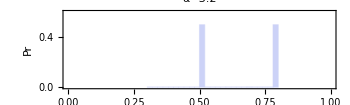
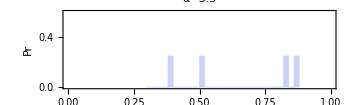
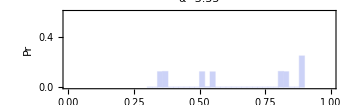
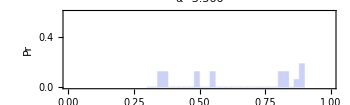
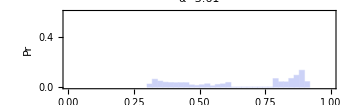
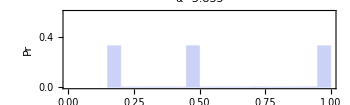
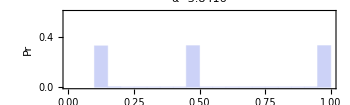
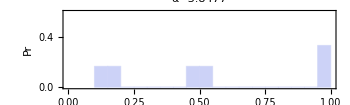

```mathematica
Row@Table[Histogram[g[x0,α,10000],20,"Probability",PlotLabel->"α="<>ToString@α,ImageSize->350,AspectRatio->0.3,AxesLabel->{"x"~Style~15,"Pr"~Style~15},PlotRange->{{0,1},{0,0.6}},AxesOrigin->{0,0},Frame->True],{α,αs}]
```

```mathematica
h[{{{x_,x_},{x_,y_}},α_}]:={{{y,y},{y,f[{y,α}][[1]]}},α};
p[x0_,α_,n_]:=(Transpose@NestList[h,{{{x0,x0},{x0,f[{x0,α}][[1]]}},α},n])[[1]]~Flatten~1;
```

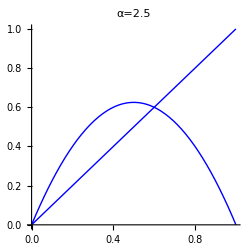
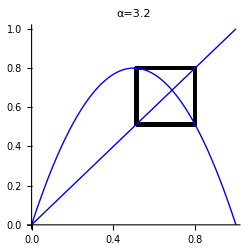
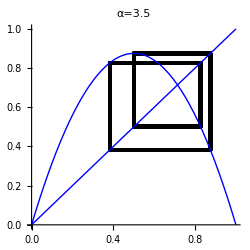
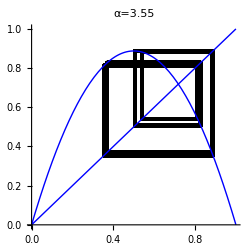
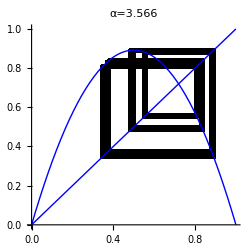
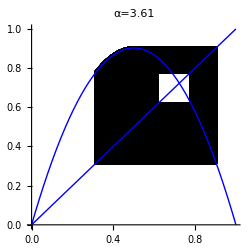
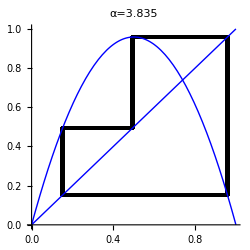
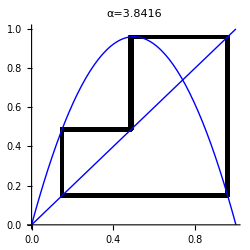

```mathematica
Row@Table[Show[
ListLinePlot[p[x0,α,10000][[9900;;]],AspectRatio->1,Frame->False,ImageSize->250,AxesOrigin->{0,0},PlotLabel->"α="<>ToString@α,PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Thickness@0.01,Black]],
Plot[x,{x,0,1},PlotStyle->Blue],
Plot[f[{x,α}][[1]],{x,0,1},PlotStyle->Blue]
],{α,{2.5}~Join~αs}]
```

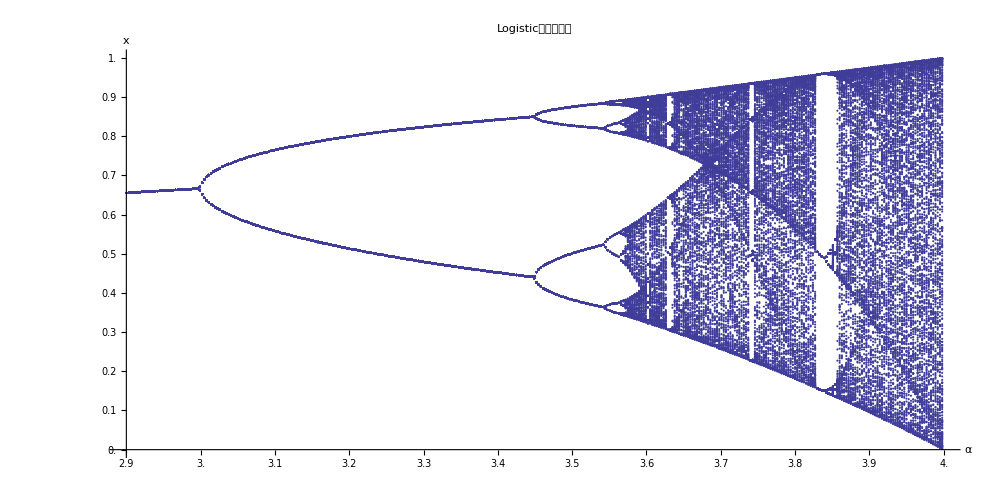

```mathematica
maxn=1000;lastn=300;minα=2.9;maxα=4;stepα=0.003;
ListPlot[Table[{α,#}&/@g[x0,α,maxn][[maxn-lastn;;]],{α,Range[minα,maxα,stepα]}]~Flatten~1,ImageSize->1000,AspectRatio->0.5,AxesLabel->{"α"~Style~20,"x"~Style~20},Ticks->{Range[minα,maxα,0.05],Range[0,1,0.1]},AxesOrigin->{minα,0},PlotLabel->"Logistic模型分叉图"~Style~20,PlotStyle->PointSize@0.0015,PlotRange->{{minα,maxα},{0,1}}]
```

```mathematica
maxn=1000;lastn=800;minλ=0.7;maxλ=1;stepλ=(maxλ-minλ)/500;
ListPlot[Table[{λ,#}&/@g[x0,λ,maxn][[maxn-lastn;;]],{λ,Range[minλ,maxλ,stepλ]}]~Flatten~1,ImageSize->1000,AspectRatio->0.5,AxesLabel->{"λ"~Style~20,"x"~Style~20},Ticks->{Range[minλ,maxλ,(maxλ-minλ)/20],Range[-1,1,0.1]},AxesOrigin->{minλ,0},PlotLabel->"λ映射分叉图"~Style~20,PlotStyle->PointSize@0.0015,PlotRange->{{minλ,maxλ},{0,1}},GridLines->{Range[minλ,maxλ,(maxλ-minλ)/20],Range[-1,1,0.1]},GridLinesStyle->Dashed]
```

-Graphics-

```mathematica
c1=0.7192;c2=0.8327;
c3=(c2-c1)/δ+c2
cinf=c1+(c2-c1)*δ/(δ-1)
```

0.857008

0.863633